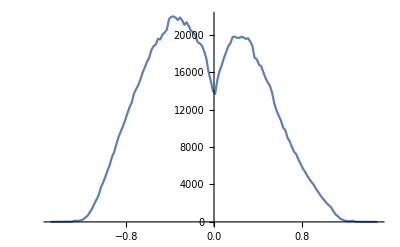

```mathematica
data=Import["C:\\Users\\hewenhao\\source\\repos\\第三次大作业II\\第三次大作业II\\line_temp_x.txt","Table"];
(*data=Table[data[[i]],{i,5,Length[data],2}];*)
Show[ListLinePlot[data,PlotRange->All]]
```

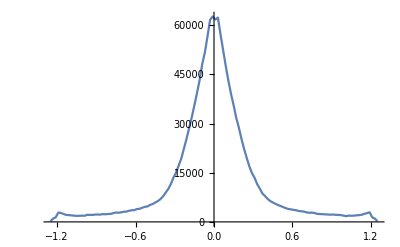

```mathematica
data2=Import["C:\\Users\\hewenhao\\source\\repos\\第三次大作业II\\第三次大作业II\\line_temp_y.txt","Table"];
(*data2=Table[data2[[i]],{i,5,Length[data2],2}];*)
Show[ListLinePlot[data2,PlotRange->All]]
```

```mathematica
datavec=Import["C:\\Users\\hewenhao\\source\\repos\\第三次大作业II\\第三次大作业II\\line_temp_vec.txt","Table"];
ListDensityPlot[datavec,PlotLegends->Automatic,ColorFunction->"Rainbow",FrameLabel->{"t_0","ω/ω_laser"}]
```

-Graphics-

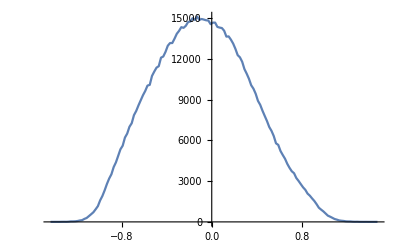

```mathematica
data2elli=Import["C:\\Users\\hewenhao\\source\\repos\\第三次大作业II\\第三次大作业II\\elli_temp_x.txt","Table"];
Show[ListLinePlot[data2elli,PlotRange->All]]
```

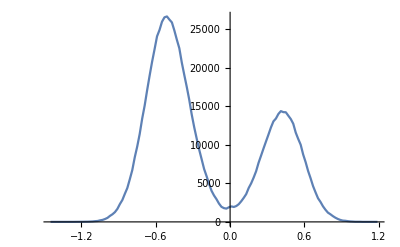

```mathematica
data2elliy=Import["C:\\Users\\hewenhao\\source\\repos\\第三次大作业II\\第三次大作业II\\elli_temp_y.txt","Table"];
Show[ListLinePlot[data2elliy,PlotRange->All]]
```

```mathematica
datavec2=Import["C:\\Users\\hewenhao\\source\\repos\\第三次大作业II\\第三次大作业II\\elli_temp_vec.txt","Table"];
ListDensityPlot[datavec2,PlotLegends->Automatic,ColorFunction->"Rainbow",FrameLabel->{"t_0","ω/ω_laser"}]
```

-Graphics-